# Funcion de correlacion

```mathematica
1+1;
SetDirectory[NotebookDirectory[]];
```

```mathematica
data=Import["data.csv","Table","FieldSeparators"-> ","];
```

```mathematica
data//TableForm;
```

```mathematica
Col1=data[[All,2]];
```

```mathematica
Col2=data[[All,3]];
```

```mathematica
Col3=data[[All,9]];
```

```mathematica
ndata=Length[data];
```

```mathematica
Min[Col1];
Max[Col1];
```

```mathematica
Min[Col3];
Max[Col3];
```

```mathematica
c=300000(*km/s*);
H0=70(*km/(s Mpc)*);
```

### escogiendo bins

```mathematica
bin1=Select[data,(0<#[[9]]<0.4)&];
```

```mathematica
Export["bin1.dat",bin1];
```

```mathematica
bin2=Select[data,(0.4<#[[9]]<0.8)&];
```

```mathematica
Export["bin2.csv",bin2];
```

```mathematica
bin3=Select[data,(0.8<#[[9]]<1.2)&];
```

```mathematica
Export["bin3.csv",bin3];
```

```mathematica
bin4=Select[data,(1.2<#[[9]]<1.6)&];
```

```mathematica
Export["bin4.csv",bin4];
```

```mathematica
bin5=Select[data,(1.6<#[[9]]<2.1)&];
```

```mathematica
Export["bin5.csv",bin5];
```

```mathematica
col1=bin5[[All,2]];
```

```mathematica
col2=bin5[[All,3]];
```

```mathematica
col3=bin5[[All,9]];
```

```mathematica
nbin1=Length[bin5]
```

260

#### poner un for: para cada i evaluar todos los j

### distancias:

#### distancia con redshift

```mathematica
For[i=1,i≤260,i++,For[j=1,j≤260,j++,dist5=Table[If[i≠j,(ArcCos[Sin[col1[[i]]]*Sin[col1[[j]]]+Cos[col1[[i]]]*Cos[col1[[j]]*Cos[col2[[i]]-col2[[j]]]]])/(H0(1+(col3[[i]]-col3[[j]]))) ,Nothing],{i,1,260},{j,1,260}]]]
```

```mathematica
Export["dist5.dat",dist5];
```

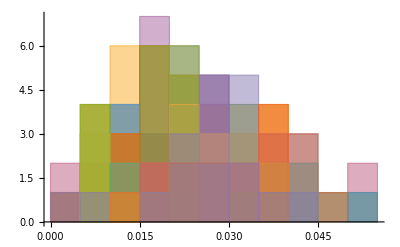

```mathematica
Histogram[dist5]
```

```mathematica
coldr=RandomSample[col1];
```

```mathematica
For[i=1,i≤260,i++,For[j=1,j≤260,j++,dist5dr=Table[If[i≠j,(ArcCos[Sin[coldr[[i]]]*Sin[coldr[[j]]]+Cos[coldr[[i]]]*Cos[coldr[[j]]*Cos[col2[[i]]-col2[[j]]]]])/(H0*(1+(col3[[i]]-col3[[j]]))),Nothing],{i,1,260},{j,1,260}]]]
```

```mathematica
Export["dist5dr.dat",dist5dr];
```

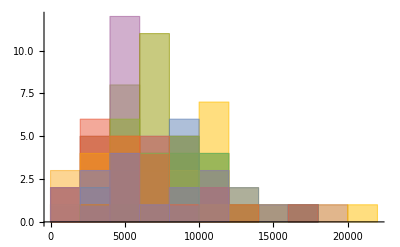

```mathematica
Histogram[dist5dr]
```

```mathematica
colrr=RandomSample[col2];
```

```mathematica
dist5dr=RandomSample[dist5];
```

```mathematica
For[i=1,i≤260,i++,For[j=1,j≤260,j++,dist5rr=Table[If[i≠j,(ArcCos[Sin[coldr[[i]]]*Sin[coldr[[j]]]+Cos[coldr[[i]]]*Cos[coldr[[j]]*Cos[colrr[[i]]-colrr[[j]]]]])*c/(H0*(1+(col3[[i]]-col3[[j]]))),Nothing],{i,1,260},{j,1,260}]]]
```

```mathematica
Export["dist5rr.dat",dist5rr]
```

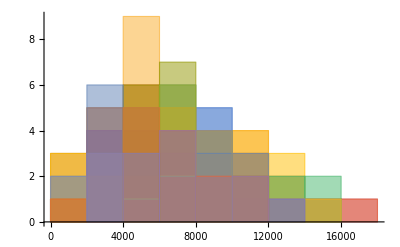

```mathematica
Histogram[dist5rr]
```

```mathematica
w=(dist5-2*dist5dr+dist5rr)/dist5rr;
```

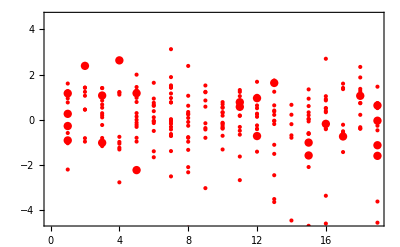

```mathematica
ListPlot[w,Mesh->All, AxesOrigin->{0,0},Axes-> False, Frame->{{True,False},{True,False}}, FrameTicks->All,ImageSize->400, PlotStyle->Red,LabelStyle->{16,GrayLevel[0],Bold}]
```